# Lecture 2 - Force Analysis

### A Puzzle...

Triangle or quadrilateral?
4 distinct points in a plane can either be arrange as a triangle with a point inside or as a quadrilateral.
Extra Brownie Points: Use the cross product in your answer

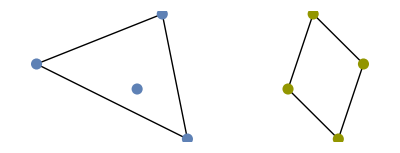

```mathematica
pts={{-2,5},{3,7},{4,2}};
pts2={1,0}+#&/@{{7,4},{8,7},{10,5},{9,2}};
centerPlot@Graphics[{Line/@Subsets[pts,{2}],Line@Append[pts2,First@pts2],color1,PointSize[0.02],Point[pts],Point[{2,4}],color2,Point[pts2]}]
```

Given 4 points p_1=(x_1,y_1), p_2=(x_2,y_2), p_3=(x_3,y_3), p_4=(x_4,y_4), how would you determine which of the above two arrangements they belong in?

Solution #1
In the left case, draw the three triangles between the inside point and the vertices of the triangle. The sum of the area of the three small triangles (which can be found using Heron’s formula) equals the area of the large triangle. Of course, you do not know which of the points is inside the triangle, so you must try this method four times assuming each point is the inside point.

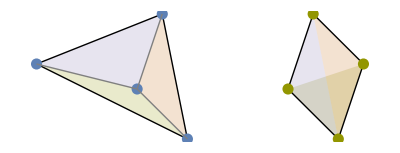

```mathematica
pts={{-2,5},{3,7},{4,2}};
pt={2,4};
pts2={1,0}+#&/@{{7,4},{8,7},{10,5},{9,2}};
centerPlot@Graphics[{{Opacity[0.2],EdgeForm[],color3,Triangle[Append[pts[[{1,2}]],pt]],color4,Triangle[Append[pts[[{2,3}]],pt]],color2,Triangle[Append[pts[[{3,1}]],pt]]},Line/@Subsets[pts,{2}],{Opacity[0.2],EdgeForm[],color2,Triangle[Append[pts2[[{3,1}]],Last@pts2]],color3,Triangle[Append[pts2[[{1,2}]],Last@pts2]],color4,Triangle[Append[pts2[[{2,3}]],Last@pts2]]},Line@Append[pts2,First@pts2],color1,PointSize[0.02],Point[pts],Point[pt],color2,Point[pts2],{Gray,Line[{pt,#}&/@pts]}}]
```

In the right case, the sum of the three triangles will always be larger than the area of the triangle defined by the three points because of the overlap in the areas.

Solution #2
Take two points and find the equation of the line L_1 going through them. Take the other two points and find the equation of the line L_2 going through them. Find the point of intersection P of L_1 and L_2. In the case of a triangle with a point inside, the P will only lie on L_1 or L_2; in the case of a quadrilateral, P will either lie on both L_1 and L_2 or on neither line.

Solution #3
Let’s go for the Brownie points! In the left case, define p_0 as the inside point and p_1, p_2, p_3 as the triangle points. Define the 3D vectors (A⃗)_1=(p⃗)_1-(p⃗)_0, (A⃗)_2=(p⃗)_2-(p⃗)_0, (A⃗)_3=(p⃗)_3-(p⃗)_0 (treating the z-component as 0). Now consider the Sign (i.e. whether the value is positive or negative) of the z-components of the cross products (A⃗)_1×(A⃗)_2, (A⃗)_2×(A⃗)_3, and (A⃗)_3×(A⃗)_1 (i.e. whether the right-hand rule points into or out of the page). Since p_4 is inside the triangle, the sign of all three z-components will be the same. As in Solution #1, you do not know which point is p_0, so you must repeat this procedure four times assuming each point is p_0 in turn.

In the case on the right, the signs of the z-components of the cross products will never all be the same (at least one will point into the board and another will point out of the board). Why? If all three cross products have the same sign then it means that you kept rotating in the same direction around your point of origin, and this is only possible if the point is inside the triangle. □

### Math Wrap-up: Applications of the Dot and Cross Product

Example (Dot Product)
Given vectors A⃗ and B⃗, define C⃗=A⃗-B⃗.

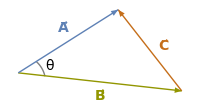

```mathematica
{color1,color2,color3}=ColorData[97][#]&/@{1,10,6};
centerPlot@Graphics[{{Text[font@"θ",{-0.53,0.19}],-Graphics-,Circle[{-0.7,0.1},0.15,{0.21,0.84}]},Thick,Arrowheads[0.07],{color2,Arrow[{{-0.7,0.15},{0.2,0.05}}]},{color3,Arrow[{{0.2,0.05},{-0.15,0.5}}]},{color1,Arrow[{{-0.7,0.15},{-0.15,0.5}}]},Text[font["A⃗",14,Italic,Bold,color1],{-0.45,0.4}],Text[font["B⃗",14,Italic,Bold,color2],{-0.25,0.02}],Text[font["C⃗",14,Italic,Bold,color3],{0.1,0.3}]},ImageSize->200]
```

Using the dot product,

C⃗·C⃗=(A⃗-B⃗)·(A⃗-B⃗)
=A⃗·A⃗-A⃗·B⃗-B⃗·A⃗+B⃗·B⃗
=(|A⃗|)^2-2A⃗·B⃗+(|B⃗|)^2
=(|A⃗|)^2+(|B⃗|)^2-2|A⃗||B⃗|Cos[θ]

where θ is the angle between A⃗ and B⃗. We have derived the Law of Cosines! □

Example (Cross Product)
Given vectors A⃗ and B⃗, we know that |A⃗×B⃗|=|A⃗||B⃗|Sin[θ] where θ is the angle between A⃗ and B⃗. If we draw the parallelogram with sides A⃗ and B⃗

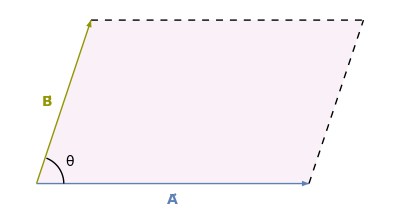

```mathematica
shrink=0.8;
{color1,color2}=ColorData[97][#]&/@{1,10};
arc[r_,{θ1_,θ2_},shift_:{0,0}]:=
Line[Table[shift+r{ Cos[θ], Sin[θ]},{θ,θ1,θ2,(θ2-θ1)/Round[((θ2-θ1)/(2π))180.]}]]
centerPlot@Graphics[{{RGBColor[0.8, 0.472, 0.72],Opacity[0.1],Polygon@{shrink{{-0.2,0.4},{-0.3,0.1},{0.2,0.1},{0.3,0.4}},{{-0.3,0.1},{0.2,0.1}}}},Text[font["A⃗",14,Italic,Bold,color1],shrink{-0.05,0.07}],Text[font["B⃗",14,Italic,Bold,color2],shrink{-0.28,0.25}],Text[font@"θ",shrink{-0.24,0.14}],Thick,{color1,Arrow[shrink{{-0.3,0.1},{0.2,0.1}}]},{color2,Arrow[shrink{{-0.3,0.1},{-0.2,0.4}}]},Thin,Dashed,Line[shrink{{{-0.2,0.4},{0.3,0.4}},{{0.2,0.1},{0.3,0.4}}}],Dashing[None],arc[shrink 0.05,{0,1.2},shrink{-0.3,0.1}]}]
```

we see that the area of this parallelogram also equals |A⃗||B⃗|Sin[θ]. Therefore, A⃗×B⃗ is the vector whose direction is given by the right-hand rule (in this case, it would be coming out of the page at you) and whose magnitude equals the area of the parallelogram with sides A⃗ and B⃗. □

#### Advanced Section: Rotating a Vector in 3D Space

In classical mechanics you often need to rotate vectors. For example, uniform circular motion will be an important concept in this course. In more advanced courses, you may encounter anything from rolling cylinders to rotating frames of reference.

In 2D, rotating a vector is not too complicated. Indeed, we have already proved the main result needed in Lecture 1’s Dot Product section: In Cartesian coordinates, rotating a point (x,y) counter-clockwise about the origin by an angle ϕ yields the point (x Cos[ϕ]-y Sin[ϕ],x Sin[ϕ]+y Cos[ϕ]).

In 3D, the situation may be much more complex. Often times we simplify matters by rotating a vector about either the x-, y-, or z-axis. But sometimes, you truly need a general formula for rotating a vector around another vector.

That is where the Rodrigues’ rotation formula comes to the rescue! This formula tells you how to rotate any vector v⃗ around an arbitrary unit vector ẑ by an angle θ clockwise (when looking in the direction of ẑ).

(v⃗)_rot=v⃗ Cos[θ]+(ẑ×v⃗)Sin[θ]+ẑ (ẑ·v⃗)(1-Cos[θ])

```mathematica
centerPlot@Manipulate[
k={Sin[kθ]Cos[kϕ],Sin[kθ]Sin[kϕ],Cos[kθ]};
vRot=v*Cos[θ]+Cross[k,v]Sin[θ]+k*(k.v)(1-Cos[θ]);
Show[Graphics3D[{Gray,Line[2{{{-1,0,0},{1,0,0}},{{0,-1,0},{0,1,0}},{{0,0,-1},{0,0,1}}}],Black,{Opacity[0.5],Arrow[{{0,0,0},v}],Text[font@"v⃗",1.15v]},Thick,Arrow[{{0,0,0},vRot}],Text[font@"(v⃗)_rot",1.17vRot],color2,Arrow[{{0,0,0},k}],Text[font@"ẑ",1.1k+{-0.25,0,-0.2}],color3,Dashed,Line[{k,4k}]},ImageSize->250,PlotRange->2{{-1,1},{-1,1},{-1,1}},ViewPoint->{0.8204967430140271,-3.25497447400264,0.4618725671596166}],ParametricPlot3D[v*Cos[t]+Cross[k,v]Sin[t]+k*(k.v)(1-Cos[t]),{t,0,2π}]]
,{{θ,0.35},0,2π},{{kθ,0.3,"k_θ"},0,π},{{kϕ,0,"k_ϕ"},0,2π}
,Initialization:>(v={1,1,1};)]
```

We will not derive Rodrigues’ rotation formula here, but Wikipedia has a simple derivation. Note that this formula is rather simple, and all it requires are the dot product and cross product.

#### Advanced Section: Cartesian vs Polar Coordinates

This section gives you a preview of what we will do in Ph 1b.

Often times you can greatly simplify a problem by working in the appropriate coordinate system. For example, polar coordinates are especially suited for describing circular motion. The equation of a circle using Cartesian coordinates is y=±√(R^2-x^2) while in polar coordinates it is simply r=R. Similarly, imagine that there is a 2D circularly symmetric force of magnitude F=r^2 which pushes you outwards and gets stronger as you go further from the origin. Using Cartesian unit vectors, we would write this force as

F⃗=(x^2+y^2)(x x̂+y ŷ)/((x^2+y^2)^(1/2))

where r^2=x^2+y^2 is the magnitude of the force and (x x̂+y ŷ)/((x^2+y^2)^(1/2)) represents the radial direction. In polar coordinates, this force takes the much simpler form

F⃗=r^2 r̂

The polar unit vectors r̂ and θ̂ are shown graphically below, and both are discussed extensively in the Math Bootcamp Coordinate Unit Vectors.

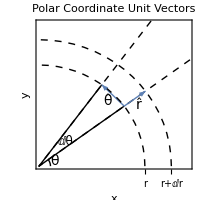

```mathematica
s=0.15;s2=0.22;r1=0.6;r2=0.75;
centerPlot@Show[RegionPlot[x>1,{x,0,1},{y,0,1},FrameLabel->(font[#,Italic]&/@{"x","y"}),PlotRange->0.85{{0,1},{0,1}},ImageSize->200,PlotRangePadding->None,FrameTicks->{{None,None},{{{r1,font["r",12]},{r2,font["r+ⅆr",12]}},None}},PlotLabel->font["Polar Coordinate Unit Vectors",12]],
Graphics[{{Dashed,Line[{{2Cos[π/4+s],2Sin[π/4+s]},{0,0},{2Cos[π/4-s],2Sin[π/4-s]}}]},Line[{{r1 Cos[π/4+s],r1 Sin[π/4+s]},{0,0},{r1 Cos[π/4-s],r1 Sin[π/4-s]}}],Circle[{0,0},0.065,{π/4-s,0}],{Thick,color1,Arrow[{{r1 Cos[π/4-s],r1 Sin[π/4-s]},{r1 Cos[π/4+s],r1 Sin[π/4+s]}}],Arrow[{{r1 Cos[π/4-s],r1 Sin[π/4-s]},{r2 Cos[π/4-s],r2 Sin[π/4-s]}}]},{Dashed,Circle[{0,0},r1 ,{0,π/2}],Circle[{0,0},r2 ,{0,π/2}]},Text[font["ⅆθ",12],{0.15,0.145}],Text[font@"θ",{0.09,0.028}],Text[font@"θ̂",0.55{Cos[π/4],Sin[π/4]}],Text[font@"r̂",(r1+r2)/2{Cos[π/4-s2],Sin[π/4-s2]}]}]]
```

One note of caution: unlike in Cartesian coordinates, where the unit vectors x̂ and ŷ always point in the same direction, the polar coordinate unit vectors r̂ and θ̂ change with the base point (r,θ) at which they are computed. This implies that the time derivatives of these unit vectors are not zero. Let’s look at an example.

Suppose we have a particle traveling on a circle of radius R centered at the origin. The position of the particle is given by

r⃗=R Cos[ω t]x̂+R Sin[ω t]ŷ

The velocity v⃗=(ⅆ r⃗)/ⅆt equals the time derivative of this vector. In Cartesian coordinates, the time derivative of a vector equals the time derivative of each of its components. Thus,

v⃗=-R ω Sin[ω t]x̂+R ω Cos[ω t]ŷ

Note that |v⃗|=ω R. We can visualize this output

```mathematica
centerPlot@Manipulate[Graphics[{{EdgeForm[color2],Opacity[0.2],color2,Disk[]},color3,Arrow[{{0,0},{Cos[θ],Sin[θ]}}],Text[font@"r⃗",1/2{Cos[θ],Sin[θ]}+0.1{-Sin[θ],Cos[θ]}],color1,Arrow[{{Cos[θ],Sin[θ]},{Cos[θ],Sin[θ]}+ω{-Sin[θ],Cos[θ]}}],Text[font@"v⃗",1.1{1/2 (2 Cos[θ]-ω Sin[θ]),1/2 (ω Cos[θ]+2 Sin[θ])}],Purple,PointSize[0.02],Point[{Cos[θ],Sin[θ]}]},PlotRange->1.3{{-1,1},{-1,1}},ImageSize->{220,Automatic},PlotLabel->font["Uniform Circular Motion: Position and Velocity",11]],{{θ,π/6},0,2π},{{ω,0.7},0.1,2}]
```

Now lets try switching polar unit vectors, where in many ways this problem will be much easier. The unit vectors are now r̂ and θ̂. The vector from the origin to the particle’s position is given by

r⃗=R r̂

with θ=ω t. What is the velocity vector? Since the particle is traveling counter-clockwise in a circle, its velocity must be in the direction θ̂. From Equation (TextNumbered), we can find its magnitude

v⃗=R ω θ̂

How can we derive Equation (TextNumbered) from Equation (TextNumbered)? The key is in remembering that in polar coordinates, the unit vectors depend on the coordinates. Thus (unlike in Cartesian coordinates) they can vary in time and have time derivatives. To compute these time derivatives, convert r̂ and θ̂ into Cartesian coordinates,

r̂=Cos[θ]x̂+Sin[θ]ŷ

θ̂=-Sin[θ]x̂+Cos[θ]ŷ

Now that we are safely back in Cartesian coordinates, we can take the time derivative and then change the result back into polar unit vectors,

(ⅆ r̂)/ⅆt=-θ̇Sin[θ]x̂+θ̇ Cos[θ]ŷ=θ̇ θ̂

(ⅆ θ̂)/ⅆt=-θ̇Cos[θ]x̂-θ̇ Sin[θ]ŷ=-θ̇ r̂

These derivatives can also be seen graphically by considering a very small motion between a point at r[t]r̂+θ[t]θ̂ and r[t+Δ,t]r̂+θ[t+Δ,t]θ̂.

With this information in hand, we can use Equation (TextNumbered) to derive Equation (TextNumbered) since

v⃗=(ⅆ r⃗)/ⅆt=ⅆ/ⅆt[R r̂]=R(ⅆ r̂)/ⅆt=R θ̇ θ̂

Because θ=ω t, θ̇=ω and hence we find the expected result v⃗=R ω θ̂.

### Playing with Forces

#### Preview

We now have (almost) all of the mathematics ready to dive into Newton’s Laws of Motion and start doing some real physics (i.e. analyzing bouncing balls, collisions, systems of pulleys). This, together with basic calculus (derivatives and integrals) opens up the world to us.

We will focus much of our attention on interesting problems, many of which are drawn from David Morin’s fabulous book Introduction to Classical Mechanics with Problems and Solutions. I cannot recommend this book highly enough!!!

#### Supplemental Section: Newton’s Laws of Motion

A Supplemental Section covers the same material that you will see in the course lectures, but with slightly different ordering and attention to different details.

And so the pure math sections end, and we delve into the meat of things. Here comes the physics!

Given a position (r⃗) of a particle, its velocity (v⃗) and acceleration (a⃗) are given by

v⃗≡(ⅆ r⃗)/ⅆt

a⃗≡(ⅆ^2 r⃗)/(ⅆ t^2)=(ⅆ v⃗)/ⅆt

The speed of an object moving with velocity v⃗ equals |v⃗|.

Newton had three very intelligent things to say about velocities and accelerations:

Newton's 1st Law: When viewed in an inertial reference frame, an object either remains at rest or continues to move at a constant velocity, unless acted upon by an external force.

Newton's 2nd Law: ∑F⃗=m a⃗
The vector sum of the forces F⃗ on an object is equal to the mass m of that object multiplied by the acceleration vector a⃗ of the object.

Newton's 3rd Law: When one body exerts a force on a second body, the second body simultaneously exerts a force equal in magnitude and opposite in direction on the first body.

#### Forces in Static Equilibrium

The simplest physical systems to consider are ones where all the objects are stationary. Hence, a⃗=0 for every object in the system, and by ∑F⃗=m a⃗ the net force on any object is zero (note that this is different from saying that all forces are zero).

∑F⃗=OverVector[0]   (static equilibrium)

Also note that the converse is not true: Just because the net force on every object is zero does not mean that every object is stationary (although it does imply that they all move with constant velocity).

There are various forces in the world, but the four most important ones for this course are:

Gravity - For now, we will work in very small scales (i.e. ≤100meters) and assume that the Earth is the perfectly flat. Earth's gravitation imposes a force on the center of mass of any object. This force points directly down towards the Earth and has magnitude

F_gravitation=m g

where g≈9.8 m/s^2 is Earth’s gravitational constant. Technically this gravitational constant varies depending on elevation, but for our purposes we will assume it equals 9.8 m/s^2 exactly (that’s a privilege of being a theorist!). Here is a fun link about defying gravity by using friction.

Normal - Any object touching a surface feels a normal force in a direction perpendicular to the surface. This normal force is typically denoted by N⃗.

Friction - An object trying to slide on a surface feels a frictional force parallel to the surface which tries to stop the sliding. There is a difference between static friction (an object is stationary but wants to slide across a surface) and kinetic friction (an object is sliding across a surface), but we will almost exclusively focus on static friction. For every surface, there is a frictional constant μ such that the maximum frictional force the surface can exert (before the object begins to slide) is μ N where N is the normal force. Therefore F_friction≤μ N (the static friction can be less than the maximum value). A frictionless surface has μ=0.

Tension - A rope (or chain, or stick...) exerts tension when pulled. If a massless rope is wrapped around frictionless objects, then the tension force it exerts is always uniform along the rope (otherwise, there would be a net force on a tiny piece of the string which would cause an infinite acceleration for that piece). When we get to pulleys with friction, the tension along the rope can vary.

#### Block on a Plane

Example
A block of mass M rests on a fixed plane with incline angle θ. Assuming the plane has frictional constant μ, what is the largest value of θ for which the block will remain still?

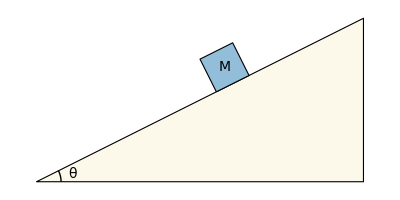

```mathematica
arc[r_,{θ1_,θ2_},shift_:{0,0}]:=
Line[Table[shift+r{ Cos[θ], Sin[θ]},{θ,θ1,θ2,(θ2-θ1)/Round[((θ2-θ1)/(2π))180.]}]]
centerPlot@Graphics[{EdgeForm[Black],{FaceForm[backgroundColor1],Polygon[{{0,0},{2,0},{2,1}}]},{FaceForm[color6],Polygon[{{1.1,0.55},{1.3,0.65},{1.2,0.85},{1.0,0.75}}]},Text[font@"M",{1.15,0.7}],Text[font@"θ",{0.22,0.045}],Thin,arc[0.15,{0,π/6-0.05}]}]
```

First, we draw the relevant forces. In this case, there is a normal force, a frictional force, and a gravitational force acting upon M.

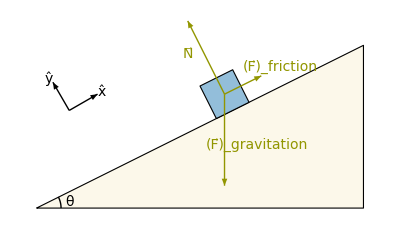

```mathematica
arc[r_,{θ1_,θ2_},shift_:{0,0}]:=
Line[Table[shift+r{ Cos[θ], Sin[θ]},{θ,θ1,θ2,(θ2-θ1)/Round[((θ2-θ1)/(2π))180.]}]]
{arrow1,arrow2,arrow3}={{{1.15,0.7},{1.15,0.7-0.5625}},{{1.15,0.7},{0.925,1.15}},{{1.15,0.7},{1.375,0.8125}}};
key={0.2,0.6};
centerPlot@Graphics[{FaceForm[],EdgeForm[Black],FaceForm[backgroundColor1],Polygon[{{0,0},{2,0},{2,1}}],FaceForm[color6],Polygon[{{1.1,0.55},{1.3,0.65},{1.2,0.85},{1.0,0.75}}],Text[font@"θ",{0.2,0.04}],{color2,Thick,Arrow[{arrow1,arrow2,arrow3}],Text[font["(F⃗)_gravitation"],Offset[{32,-5},Mean@arrow1]],Text[font["N⃗"],Offset[{-18,4},Mean@arrow2]],Text[font["(F⃗)_friction"],Offset[{37,18},Mean@arrow3]]},Thin,arc[0.15,{0,π/6-0.05}],Arrowheads[Small],Arrow[{{key,RotationTransform[π/6,key][key+{0.2,0}]},{key,RotationTransform[π/6,key][key+{0,0.2}]}}],Text[font@"x̂",RotationTransform[π/6,key][key+{0.23,0}]],Text[font@"ŷ",RotationTransform[π/6,key][key+{-0.01,0.23}]]}]
```

There are two ways to orient the axes for these problems: 1) with x̂ oriented along the inclined plane or 2) with x̂ oriented horizontally. We will use the former because it makes accounting for the normal and friction forces very straightforward, although either method is valid.

By definition, the gravitational force has magnitude M g. In our coordinate system,

(F⃗)_gravitation=-M g Sin[θ] x̂-M g Cos[θ] ŷ

and we can check that for θ=0 we do indeed regain the expected force M g straight down towards the Earth. Therefore, we can write the ∑F⃗=m a⃗ equations in the x̂- and ŷ-directions. Denoting F_friction≡|(F⃗)_friction| and recalling that a⃗=0,

0=-M g Sin[θ] +F_friction

0=-M g Cos[θ]+N

Thus N=M g Cos[θ] while F_friction=M g Sin[θ]. However, to remain in static equilibrium, F_friction≤μ N=μ M g Cos[θ]. Therefore,

M g Sin[θ]≤μ M g Cos[θ]

which simplifies to

Tan[θ]≤μ

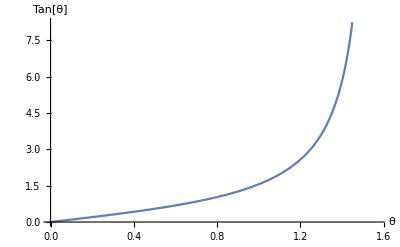

```mathematica
centerPlot@Plot[Tan[θ],{θ,0,π/2},AxesLabel->font/@{"θ","Tan[θ]"}]
```

Looking at the plot of Tan[θ], we see that we can increase θ up until Tan[θ]=μ, and increasing θ any further after that point would cause the block to slide. In fact, for any finite μ, there is some critical value of θ past which the block will begin to slide.

It is always useful to consider different limits to make sure our answer makes sense. If μ=0 (implying that the surface is frictionless), then any non-zero angle θ would cause the block to slip, as expected. If μ→∞, then the block will not slide for any value of θ<π/2. However, for θ=π/2 the block must slide, regardless of how large μ is, because the normal force goes to zero and hence so does the maximum frictional force exerted by the plane. □

### Torques

Given a force F⃗, we define the torque τ⃗ about a point O as

τ⃗=r⃗×F⃗

where r⃗ is the vector from O to the base of vector F⃗. From our definition of the cross product

|τ⃗|=|r⃗×F⃗|=|r⃗||F⃗|Sin[θ]=|r⃗||(F⃗)_⊥|

where (F⃗)_⊥ is the component of F⃗ that is perpendicular to r⃗.

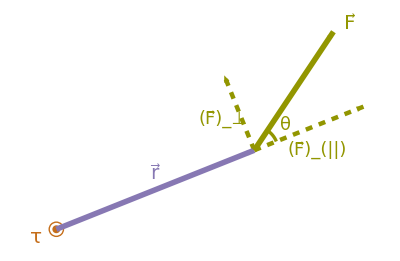

```mathematica
arc[r_,{θ1_,θ2_},{x_:0,y_:0}]:=Line[Table[{x,y}+r{Cos[θ],Sin[θ]},{θ,θ1,θ2,(θ2-θ1)/Round[((θ2-θ1)/(2π))180.]}]]
ft=Style[#,20,FontFamily->"Times"]&;
ft2=Style[#,18,FontFamily->"Times"]&;
p1={5,2};p2={2,3};
centerPlot@Graphics[{{color4,Text[ft@"τ",{-0.5,-0.2}],Disk[{0,0},0.1],Circle[{0,0},0.18]},Thickness[0.01],Arrowheads[0.06],{color3,Text[ft@"r⃗",p1/2+{0,0.4}],Arrow[{{0,0},p1}]},{color2,Text[ft@"F⃗",p1+p2+{0.4,0.2}],Text[ft2@"(F⃗)_(||)",p1+{1.6,0.0}],Text[ft2@"(F⃗)_⊥",p1+{-0.8,0.8}],Text[ft2@"θ",p1+{0.8,0.65}],Arrow[{p1,p1+p2}],{Thickness[0.006],arc[0.6,{ArcTan@@p1,ArcTan@@p2},p1]},{Dashed,Thickness[0.008],Arrowheads[0.045],Arrow[{p1,p1+(p1.p2)/Norm[p1] p1/Norm[p1]}],Arrow[{p1,p1+(p2-(p1.p2)/Norm[p1] p1/Norm[p1])}]}}}]
```

(F⃗)_(||) is the magnitude of F⃗ that lies along r⃗. Defining the unit vector r̂=(r⃗)/(|r⃗|), we find (F⃗)_(||)=F⃗·r̂. As a vector, we can write this as

(F⃗)_(||)=(F⃗·r̂)r̂

Thus, (F⃗)_⊥ must satisfy

(F⃗)_⊥=F⃗-(F⃗)_(||)=F⃗-(F⃗·r̂)r̂

(As a quick check, we see that (F⃗)_⊥·r̂=F⃗·r̂-(F⃗·r̂)(r̂·r̂)=F⃗·r̂-F⃗·r̂=0, as expected.)

Notice that the magnitude of the torque depends on the origin (which controls r⃗). Therefore, you must always state about which base point you calculate torque. However, as we next show, in static equilibrium ∑τ⃗=OverVector[0] regardless of which base point is chosen for the torques

#### Proof that ∑τ⃗=OverVector[0] in Static Equilibrium

Lemma Consider a system of point masses m_1,m_2... m_n with positions (r⃗)_1,(r⃗)_2...(r⃗)_n and velocities (v⃗)_1,(v⃗)_2...(v⃗)_n. We define the quantity

L⃗=∑_(j=1)^n m_j(r⃗)_j×(v⃗)_j

Later, we will define L⃗ as the total angular momentum of the system, but for now just treat it as a mathematical definition. Here is a possible diagram with n=3 particles.

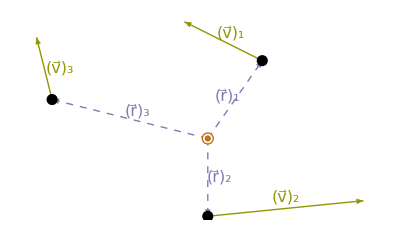

```mathematica
p1={0.7,1};p2={0,-1};p3={-2,0.5};
v1={-1,0.5};v2={2,0.2};v3={-0.2,0.8};
zero={0,0};
centerPlot@Graphics[{Thick,color2,Arrow[{{p1,p1+v1},{p2,p2+v2},{p3,p3+v3}}],Text[font["(v⃗)_1",16],Mean[{p1,p1+v1}]+{0.1,0.1}],Text[font["(v⃗)_2",16],Mean[{p2,p2+v2}]+{0,0.15}],Text[font["(v⃗)_3",16],Mean[{p3,p3+v3}]+{0.2,0}],color3,Dashed,Arrow[{{zero,p1},{zero,p2},{zero,p3}}],Text[font["(r⃗)_1",16],Mean[{zero,p1}]+{-0.1,0.05}],Text[font["(r⃗)_2",16],Mean[{zero,p2}]+{0.15,0}],Text[font["(r⃗)_3",16],Mean[{zero,p3}]+{0.1,0.1}],{Black,PointSize[0.02],Point[{p1,p2,p3}]},{White,Disk[{0,0},0.07],color4,Dashing[None],Thickness[Medium],Disk[{0,0},0.04],Circle[{0,0},0.07]}}]
```

Taking the derivative of L⃗ with respect to time,

(ⅆ L⃗)/ⅆt=∑_(j=1)^n (m_j(ⅆ(r⃗)_j)/ⅆt×(v⃗)_j+m_j(r⃗)_j×(ⅆ(v⃗)_j)/ⅆt)
=∑_(j=1)^n (m_j(v⃗)_j×(v⃗)_j+m_j(r⃗)_j×(a⃗)_j)
=∑_(j=1)^n ((r⃗)_j×(F⃗)_j)
=∑_(j=1)^n (τ⃗)_j

where in the third step we used the fact that (v⃗)_j×(v⃗)_j=OverVector[0] and (F⃗)_j=m_j(a⃗)_j. We never used the fact that there were only 3 particles, so this Lemma holds for any number n of particles, and thus for any objects whatsoever. Therefore, (ⅆ L⃗)/ⅆt equals the sum of torques (a.k.a. the net torque) for the system. □

In the case of static equilibrium where (v⃗)_j=OverVector[0] for all masses, the quantity L⃗=∑_(j=1)^n m_j(r⃗)_j×(v⃗)_j=OverVector[0] so that (ⅆ L⃗)/ⅆt=OverVector[0]. By the Lemma above, this implies that the sum of torques ∑τ⃗=OverVector[0]. Note that this statement is irrespective of the base point that we used to calculate the torques, so in this special case any base point for torque will work equally well. In other words,

In static equilibrium, both the sum of forces ∑F⃗=OverVector[0] and the sum of torques ∑τ⃗=OverVector[0]

#### Torques on a Seesaw

Let’s consider the consequences of ∑τ⃗=OverVector[0] in static equilibrium. Think back onto the seesaw example from last time. A brother with weight m_1 g is exactly balancing his bigger sister, whose weight is m_2 g, on a seesaw.

-Graphics-

The direction vector between the fulcrum and the m_1 g (-ŷ) force is (r⃗)_1=-d_1 x̂, while the direction vector between the fulcrum and the m_2 g (-ŷ) force is (r⃗)_2=d_2 x̂. Defining the right-handed coordinate system with ẑ pointing out of the page (so that x̂×ŷ=ẑ), the sum of torques equals

(τ⃗)_1+(τ⃗)_2=OverVector[0]

(r⃗)_1×(-m_1g ŷ)+(r⃗)_2×(-m_2g ŷ)=OverVector[0]

(d_1 m_1 g-d_2 m_2 g)ẑ=OverVector[0]

In this problem, as in most problems that we will consider in this course, the direction of rotation is one-dimensional (i.e. all torques either point into or out of the page), so that the torque equation simply becomes a balance between torques rotating an object clockwise and the torques rotating that same object counter-clockwise,

d_1 m_1 g-d_2 m_2 g=0

d_1 m_1-d_2 m_2=0

which is the condition for the system to be in static equilibrium.s

What if we had instead chosen the location on the seesaw where the big sister sits as our base point for calculating torque? In that case, (r⃗)_2=OverVector[0], so how will the (even larger) torque from the little brother be balanced, given by (r⃗)_1×(-m_1g ŷ)=(d_1+d_2)m_1 g ẑ?

Our drawing above is a bit misleading, since we neglected the normal force on the fulcrum of the seesaw (we previously neglected this normal force since it has zero torque when using the fulcrum as our base point for torque). Since ∑F⃗=OverVector[0] in static equilibrium, the normal force at the fulcrum must equal (F⃗)_3=(m_1+m_2)g ŷ and its distance from the big sister is (r⃗)_3=-d_2 x̂. Therefore, the torque equation using the big sister’s seat as the base point yields

(τ⃗)_1+(τ⃗)_2+(τ⃗)_3=OverVector[0]

(d_1+d_2)m_1 g ẑ+0-d_2(m_1+m_2)g ẑ=OverVector[0]

d_1 m_1-d_2 m_2=0

as found above! As a final note, you are invited to rework this problem when the seesaw is not flat but rather at an angle θ. In this case, you can show that the exact same solution, namely d_2=m_1/m_2 d_1, will yield static equilibrium. This implies that if you situate the brother and sister as shown above, you can move the seesaw into whatever position you want and it will stay there!  □

#### Calculating Torque - Multiple Methods

Let’s recap some ways to calculate torques τ⃗=r⃗×F⃗. As a specific example, we consider a ladder of length d leaning against a frictionless wall. The coefficient of friction with the ground is μ.

What is the torque (τ⃗)_(m g) from the m g⃗ acting on the center of mass (i.e. the middle) of the ladder, using the ground as the point of origin for the torque (brown point at the base of the ladder)?

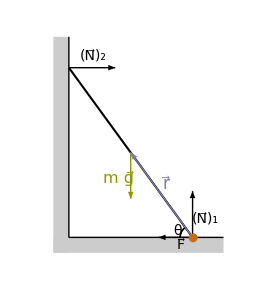

```mathematica
arc[r_,{θ1_,θ2_},shift_:{0,0}]:=
Line[Table[shift+r{ Cos[θ], Sin[θ]},{θ,θ1,θ2,(θ2-θ1)/Round[((θ2-θ1)/(2π))180.]}]]
centerPlot@Show[Graphics@@{{arc[0.04,{2.2,π},{0.15,-0.25}],{arc[0.04,{2.2,π},{0.15,-0.25}],{{GrayLevel[0.8],Polygon[{{-0.3,-0.25},{-0.3,-0.3},{0.25,-0.3},{0.25,-0.25}}]},{GrayLevel[0.8],Polygon[{{-0.25,0.4},{-0.25,-0.3},{-0.3,-0.3},{-0.3,0.4}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[{}],Line[{{-0.25,-0.25},{0.25,-0.25}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[{}],Line[{{-0.25,0.4},{-0.25,-0.25}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[1.5],AbsoluteDashing[{}],Line[{{-0.25,0.3},{0.15,-0.25}}]}}}},PlotRangePadding->None,PlotRange->{{-0.39,0.35},{-0.37,0.43}},ImageSize->280},
base={0.15,-0.3};
pt1={-0.05,0.025};
pt2={-0.25,0.3};
ft=16;
Graphics[{Thickness[Large],
Text[font@"θ",{0.1,-0.23}],Arrow[{base+{0,0.05},{0.04,-0.25}}],Text[font@"F⃗",{0.11,-0.276}],Arrow[{pt2,{-0.1,0.3}}],Text[font@"(N⃗)_2",{-0.17,0.34}],color2,{Arrow[{pt1,{-0.05,-0.125}}]},Text[font["m g⃗",16],{-0.09,-0.06}],Black,Arrow[{base+{0,0.05},{0.15,-0.1}}],Text[font@"(N⃗)_1",{0.19,-0.19}],color3,Arrow[{base+{0,0.05},pt1}],Text[font["r⃗",17],Mean[{base+{0,0.05},pt1}]+{0.015,0.035}],{{White,Disk[base+{0,0.05},0.012]},color4,PointSize[0.02],Point[base+{0,0.05}],Thickness[Medium],Circle[base+{0,0.05},0.012]}
}]
]
```

Method 1
The best (and most visual) method to compute the torque from m g⃗ is to break up that force into a component parallel to r⃗ (denoted m (g⃗)_(||)) and perpendicular to r⃗ (denoted m (g⃗)_⊥), as shown below.

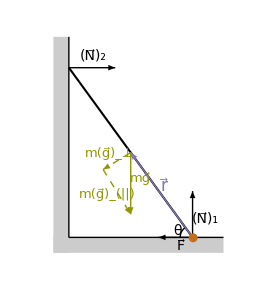

```mathematica
arc[r_,{θ1_,θ2_},shift_:{0,0}]:=
Line[Table[shift+r{ Cos[θ], Sin[θ]},{θ,θ1,θ2,(θ2-θ1)/Round[((θ2-θ1)/(2π))180.]}]]
centerPlot@Show[Graphics@@{{arc[0.04,{2.2,π},{0.15,-0.25}],{{GrayLevel[0.8],Polygon[{{-0.3,-0.25},{-0.3,-0.3},{0.25,-0.3},{0.25,-0.25}}]},{GrayLevel[0.8],Polygon[{{-0.25,0.4},{-0.25,-0.3},{-0.3,-0.3},{-0.3,0.4}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[{}],Line[{{-0.25,-0.25},{0.25,-0.25}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[{}],Line[{{-0.25,0.4},{-0.25,-0.25}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[1.5],AbsoluteDashing[{}],Line[{{-0.25,0.30000000000000004},{0.15000000000000002,-0.25}}]}}},PlotRangePadding->None,PlotRange->{{-0.39,0.35000000000000003},{-0.37,0.43}},ImageSize->280},
base={0.15,-0.3};
pt1={-0.05,0.025};
pt2={-0.25,0.3};
ft=13;

r1=pt1-base;
f1=base-{0.15,-0.1};
par1=(r1.f1)/Norm[r1] r1/Norm[r1];
per1=f1-(r1.f1)/Norm[r1] r1/Norm[r1];

Graphics[{Thickness[Large],Text[font@"θ",{0.1,-0.23}],Arrow[{base+{0,0.05},{0.04,-0.25}}],Text[font@"F⃗",{0.11,-0.277}],Arrow[{pt2,{-0.1,0.3}}],Text[font@"(N⃗)_2",{-0.17,0.34}],color2,{Arrow[{pt1,pt1+f1}],Dashed,Arrow[{pt1,pt1+per1}],Arrow[{pt1+per1,pt1+per1+par1}]},Text[font["mg⃗",ft],{-0.02,-0.06}],Text[font["m(g⃗)_⊥",ft],Mean[{pt1,pt1+per1}]+2.4{-0.01,0.01}],Text[font["m(g⃗)_(||)",ft],Mean[{pt1+per1,pt1+per1+par1}]+{-0.03,-0.01}],Black,Arrow[{base+{0,0.05},{0.15,-0.1}}],Text[font@"(N⃗)_1",{0.19,-0.19}],color3,Arrow[{base+{0,0.05},pt1}],Text[font["r⃗",17],Mean[{base+{0,0.05},pt1}]+{0.01,0.03}],{{White,Disk[base+{0,0.05},0.012]},color4,PointSize[0.02],Point[base+{0,0.05}],Thickness[Medium],Circle[base+{0,0.05},0.012]}
}]
]
```

Recall that |τ⃗|=|r⃗||F⃗|Sin[θ] so that

r⃗×(m g⃗)=r⃗×(m (g⃗)_(||)+m (g⃗)_⊥)=r⃗×(m (g⃗)_(||))+r⃗×(m (g⃗)_⊥)=r⃗×(m(g⃗)_⊥)

In other words, when calculating torque, we only need to consider the component of the force perpendicular to the point of origin r⃗ of that force!

Since the ladder has length d, we find |r⃗|=d/2. From the diagram above we also find |(g⃗)_⊥|=g Cos[θ]. Therefore, the magnitude of the torque from m g⃗ is given by

τ_(m g)=|r⃗×(m(g⃗)_⊥)|=m|r⃗||(g⃗)_⊥|=d/2 m g Cos[θ]

Recall that torque is really a vector, and its direction (using the right-hand rule) would be pointing out of the page.

Method 2
As a sanity check, we could compute the torque using

τ_(m g)=|r⃗×(m g⃗)|=m|r⃗||g⃗|Sin[θ̃]

where θ̃ is the angle between r⃗ and g⃗. The diagram below shows that θ̃=θ+π/2.

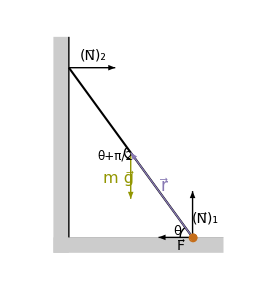

```mathematica
arc[r_,{θ1_,θ2_},shift_:{0,0}]:=
Line[Table[shift+r{ Cos[θ], Sin[θ]},{θ,θ1,θ2,(θ2-θ1)/Round[((θ2-θ1)/(2π))180.]}]]
centerPlot@Show[Graphics@@{{arc[0.04,{2.2,π},{0.15,-0.25}],{{GrayLevel[0.8],Polygon[{{-0.3,-0.25},{-0.3,-0.3},{0.25,-0.3},{0.25,-0.25}}]},{GrayLevel[0.8],Polygon[{{-0.25,0.4},{-0.25,-0.3},{-0.3,-0.3},{-0.3,0.4}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[0.1],AbsoluteDashing[{}],Line[{{-0.25,-0.25},{0.25,-0.25}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[{}],Line[{{-0.25,0.4},{-0.25,-0.25}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[1.5],AbsoluteDashing[{}],Line[{{-0.25,0.30000000000000004},{0.15000000000000002,-0.25}}]}}},PlotRangePadding->None,PlotRange->{{-0.39,0.35000000000000003},{-0.37,0.43}},ImageSize->280},
base={0.15,-0.3};
pt1={-0.05,0.025};
pt2={-0.25,0.3};
ft=16;
Graphics[{
arc[0.02,{2.2,3π/2},pt1],Thickness[Large],
Text[font["θ",13],{0.1,-0.23}],Text[font["θ+π/2",12],{0.1,-0.26}+pt1-(base+{0,0.05})],Arrow[{base+{0,0.05},{0.04,-0.25}}],Text[font@"F⃗",{0.11,-0.277}],Arrow[{pt2,{-0.1,0.3}}],Text[font@"(N⃗)_2",{-0.17,0.34}],color2,{Arrow[{pt1,{-0.05,-0.125}}]},Text[font["m g⃗",ft],{-0.09,-0.06}],Black,Arrow[{base+{0,0.05},{0.15,-0.1}}],Text[font@"(N⃗)_1",{0.19,-0.19}],color3,Arrow[{base+{0,0.05},pt1}],Text[font["r⃗",17],Mean[{base+{0,0.05},pt1}]+{0.01,0.03}],{{White,Disk[base+{0,0.05},0.012]},color4,PointSize[0.02],Point[base+{0,0.05}],Thickness[Medium],Circle[base+{0,0.05},0.012]}
}]
]
```

This implies that the torque has magnitude

τ_(m g)=d/2 m g Sin[θ+π/2]
=d/2 m g Cos[θ]

as found above.

Special Limits
Once you have an answer for the torque, double check this answer in the limiting cases θ=0 and θ=π/2:

Case 1  θ=0
The ladder is flat on the ground, so gravity should be giving the maximum possible torque. Since r⃗ and m g⃗ are perpendicular, the torque will have magnitude τ_(m g)=|r⃗||m g⃗|=d/2 m g.

Case 2  θ=π/2
The ladder points vertically against the wall. Since m g⃗ passes right through the point we are calculating torque about, the torque from m g⃗ equals zero, τ_(m g)=0.

#### Leaning Ladder

Example
A ladder leans against a frictionless wall. The coefficient of friction with the ground is μ. What is the smallest angle the ladder can make with the ground and not slip?

Solution
Before starting this problem, let us build our intuition on when the ladder should slip. When θ=π/2, the ladder is standing upright and will never fall, even if μ=0. As θ decreases, it becomes more difficult for the ladder to stay upright (think about your own experience when leaning against a wall - if you make a smaller angle θ with the floor, it gets much tougher to not fall). No matter how large μ is, we expect that any ladder will fall when θ≈0.

Now let us get quantitative. First, we draw the forces on the system. Note that gravity always acts on the center of mass of an object, which in this case is the midpoint of the ladder.

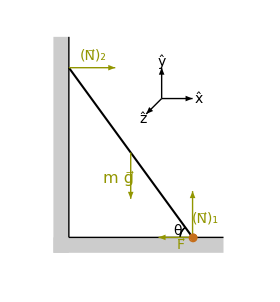

```mathematica
arc[r_,{θ1_,θ2_},shift_:{0,0}]:=
Line[Table[shift+r{ Cos[θ], Sin[θ]},{θ,θ1,θ2,(θ2-θ1)/Round[((θ2-θ1)/(2π))180.]}]]
centerPlot@Show[Graphics@@{{arc[0.04,{2.2,π},{0.15,-0.25}],{arc[0.04,{2.2,π},{0.15,-0.25}],{{GrayLevel[0.8],Polygon[{{-0.3,-0.25},{-0.3,-0.3},{0.25,-0.3},{0.25,-0.25}}]},{GrayLevel[0.8],Polygon[{{-0.25,0.4},{-0.25,-0.3},{-0.3,-0.3},{-0.3,0.4}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[{}],Line[{{-0.25,-0.25},{0.25,-0.25}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[{}],Line[{{-0.25,0.4},{-0.25,-0.25}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[1.5],AbsoluteDashing[{}],Line[{{-0.25,0.3},{0.15,-0.25}}]}}}},PlotRangePadding->None,PlotRange->{{-0.39,0.35},{-0.37,0.43}},ImageSize->280},
base={0.15,-0.3};
pt1={-0.05,0.025};
pt2={-0.25,0.3};
ft=16;
Graphics[{directionVectors[{0.05,0.2},1],Thickness[Large],
Text[font@"θ",{0.1,-0.23}],color2,Arrow[{base+{0,0.05},{0.04,-0.25}}],Text[font@"F⃗",{0.11,-0.276}],Arrow[{pt2,{-0.1,0.3}}],Text[font@"(N⃗)_2",{-0.17,0.34}],{Arrow[{pt1,{-0.05,-0.125}}]},Text[font["m g⃗",16],{-0.09,-0.06}],Arrow[{base+{0,0.05},{0.15,-0.1}}],Text[font@"(N⃗)_1",{0.19,-0.19}],{{White,Disk[base+{0,0.05},0.012]},color4,PointSize[0.02],Point[base+{0,0.05}],Thickness[Medium],Circle[base+{0,0.05},0.012]}
}]
]
```

Balancing forces in the x- and y-directions yields

N_1=m g

N_2=F≤μ N_1=μ m g

Lastly, we must balance the torques in the system. Note that we are free to choose any origin to calculate the torque τ⃗=r⃗×F⃗ around, and because OverVector[0]×F⃗=OverVector[0], any forces at the origin we will not be factored into the torque. Therefore, one excellent choice for an origin is the base point of the ladder, which excludes N_1 and F from our calculation (of course, you could choose any point that you want, but the computation would be a bit tougher).

The length of the ladder was not specified in the problem (which means it will drop out of the final answer), so let us denote the length of the ladder by d. The torque of the m g⃗ force (below, left) is given by d/2 m g Cos[θ] ẑ where ẑ points out of the page. Similarly, the torque of the (N⃗)_2 force (below, right) equals d N_2 Sin[θ] (-ẑ). The two remaining forces, F⃗ and (N⃗)_1, have zero torque about the base point we chose.

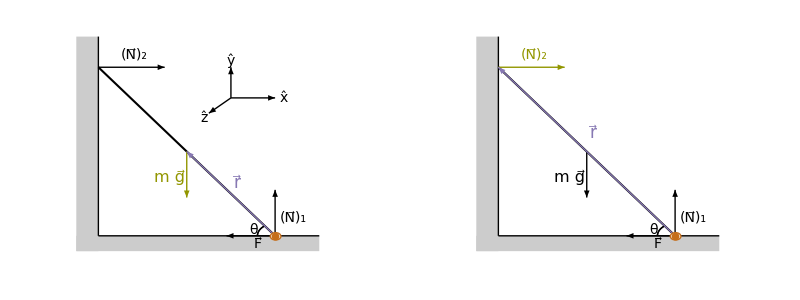

```mathematica
arc[r_,{θ1_,θ2_},shift_:{0,0}]:=
Line[Table[shift+r{ Cos[θ], Sin[θ]},{θ,θ1,θ2,(θ2-θ1)/Round[((θ2-θ1)/(2π))180.]}]]
plot1=Show[Graphics@@{{arc[0.04,{2.2,π},{0.15,-0.25}],{arc[0.04,{2.2,π},{0.15,-0.25}],{{GrayLevel[0.8],Polygon[{{-0.3,-0.25},{-0.3,-0.3},{0.25,-0.3},{0.25,-0.25}}]},{GrayLevel[0.8],Polygon[{{-0.25,0.4},{-0.25,-0.3},{-0.3,-0.3},{-0.3,0.4}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[{}],Line[{{-0.25,-0.25},{0.25,-0.25}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[{}],Line[{{-0.25,0.4},{-0.25,-0.25}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[1.5],AbsoluteDashing[{}],Line[{{-0.25,0.3},{0.15,-0.25}}]}}}},PlotRangePadding->None,PlotRange->{{-0.39,0.35},{-0.37,0.43}},ImageSize->280},
base={0.15,-0.3};
pt1={-0.05,0.025};
pt2={-0.25,0.3};
ft=16;
Graphics[{directionVectors[{0.05,0.2},1],Thickness[Large],
Text[font@"θ",{0.1,-0.23}],Arrow[{base+{0,0.05},{0.04,-0.25}}],Text[font@"F⃗",{0.11,-0.276}],Arrow[{pt2,{-0.1,0.3}}],Text[font@"(N⃗)_2",{-0.17,0.34}],color2,{Arrow[{pt1,{-0.05,-0.125}}]},Text[font["m g⃗",16],{-0.09,-0.06}],Black,Arrow[{base+{0,0.05},{0.15,-0.1}}],Text[font@"(N⃗)_1",{0.19,-0.19}],color3,Arrow[{base+{0,0.05},pt1}],Text[font["r⃗",17],Mean[{base+{0,0.05},pt1}]+{0.015,0.035}],{{White,Disk[base+{0,0.05},0.012]},color4,PointSize[0.02],Point[base+{0,0.05}],Thickness[Medium],Circle[base+{0,0.05},0.012]}
}]
];
plot2=Show[Graphics@@{{arc[0.04,{2.2,π},{0.15,-0.25}],{arc[0.04,{2.2,π},{0.15,-0.25}],{{GrayLevel[0.8],Polygon[{{-0.3,-0.25},{-0.3,-0.3},{0.25,-0.3},{0.25,-0.25}}]},{GrayLevel[0.8],Polygon[{{-0.25,0.4},{-0.25,-0.3},{-0.3,-0.3},{-0.3,0.4}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[{}],Line[{{-0.25,-0.25},{0.25,-0.25}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[{}],Line[{{-0.25,0.4},{-0.25,-0.25}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[1.5],AbsoluteDashing[{}],Line[{{-0.25,0.3},{0.15,-0.25}}]}}}},PlotRangePadding->None,PlotRange->{{-0.39,0.35},{-0.37,0.43}},ImageSize->280},
base={0.15,-0.3};
pt1={-0.05,0.025};
pt2={-0.25,0.3};
ft=16;
Graphics[{Thickness[Large],
Text[font@"θ",{0.1,-0.23}],Arrow[{base+{0,0.05},{0.04,-0.25}}],Text[font@"F⃗",{0.11,-0.276}],{color2,Arrow[{pt2,{-0.1,0.3}}],Text[font@"(N⃗)_2",{-0.17,0.34}]},{Arrow[{pt1,{-0.05,-0.125}}]},Text[font["m g⃗",16],{-0.09,-0.06}],Black,Arrow[{base+{0,0.05},{0.15,-0.1}}],Text[font@"(N⃗)_1",{0.19,-0.19}],color3,Arrow[{base+{0,0.05},2(pt1-(base+{0,0.05}))+base+{0,0.05}}],Text[font["r⃗",17],Mean[{base+{0,0.05},2(pt1-base)+base}]+{0.015,0.035}],{{White,Disk[base+{0,0.05},0.012]},color4,PointSize[0.02],Point[base+{0,0.05}],Thickness[Medium],Circle[base+{0,0.05},0.012]}
}]
];
centerPlot@Grid[{{plot1,plot2}},Spacings->5]
```

Therefore, the sum of torques equals

∑τ⃗=OverVector[0]=(d/2 m g Cos[θ]-d N_2 Sin[θ])ẑ

This gives us a relation for N_2,

N_2=(m g)/(2Tan[θ])

Substituting into Equation (TextNumbered), we obtain

(m g)/(2Tan[θ])=N_2≤μ m g

or equivalently

1/(2μ)≤Tan[θ]

Therefore, the ladder will just barely not slip when Tan[θ]=1/(2μ), and for all smaller values of θ the ladder would slip.

However, there is an even more clever choice of our origin to compute the torque on the ladder. In total there are three forces acting on the ladder: a normal force at the top end, gravity in the middle, and a third force -F x̂+N_1 ŷ at the base of the ladder. Denote the origin (0,0) as the bottom-left corner. Then extending lines through the normal force at the top of the ladder and gravity’s force in the middle yields an intersection point at (d/2 Cos[θ],d Sin[θ]). What if we put our origin for the calculation of torque here? Because the top normal and gravity pass through this point, their contribution to the overall torque equals 0. And since there is only one other force acting on the ladder (-F x̂+N_1 ŷ), and the net torque must equal 0, then -F x̂+N_1 ŷ must pass through this point as well.

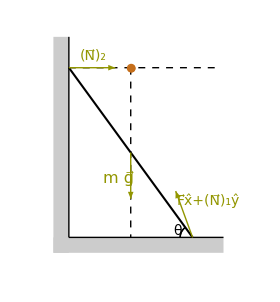

```mathematica
arc[r_,{θ1_,θ2_},shift_:{0,0}]:=
Line[Table[shift+r{ Cos[θ], Sin[θ]},{θ,θ1,θ2,(θ2-θ1)/Round[((θ2-θ1)/(2π))180.]}]]
centerPlot@Show[Graphics@@{{arc[0.04,{2.2,π},{0.15,-0.25}],{arc[0.04,{2.2,π},{0.15,-0.25}],{{GrayLevel[0.8],Polygon[{{-0.3,-0.25},{-0.3,-0.3},{0.25,-0.3},{0.25,-0.25}}]},{GrayLevel[0.8],Polygon[{{-0.25,0.4},{-0.25,-0.3},{-0.3,-0.3},{-0.3,0.4}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[{}],Line[{{-0.25,-0.25},{0.25,-0.25}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[{}],Line[{{-0.25,0.4},{-0.25,-0.25}}]},{Arrowheads[Medium],CapForm["Butt"],-Graphics-,Opacity[1],AbsoluteThickness[1.5],AbsoluteDashing[{}],Line[{{-0.25,0.3},{0.15,-0.25}}]}}}},PlotRangePadding->None,PlotRange->{{-0.39,0.35},{-0.37,0.43}},ImageSize->280},
base={0.15,-0.3};
pt1={-0.05,0.025};
pt2={-0.25,0.3};
pt3={-0.05,0.3};
ft=16;
Graphics[{{Dashed,Line[{{pt3,pt3-{0,Last@pt3+0.25}},{{-0.25,Last@pt3},{0.23,Last@pt3}}(*,{pt3,{0.15,-0.25}}*)}]},Thickness[Large],
Text[font@"θ",{0.1,-0.23}],color2,Arrow[{pt2,{-0.1,0.3}}],Text[font@"(N⃗)_2",{-0.17,0.34}],{Arrow[{pt1,{-0.05,-0.125}}]},Text[font["m g⃗",16],{-0.09,-0.06}],Arrow[{base+{0,0.05},{0.0954,-0.1}}],Text[font@"F⃗x̂+(N⃗)_1ŷ",{0.2,-0.13}],{{White,Disk[pt3,0.012]},color4,PointSize[0.02],Point[pt3],Thickness[Medium],Circle[pt3,0.012]}
}]
]
```

Using similar triangles, this implies that

N_1/F=(d Sin[θ])/(d/2 Cos[θ])=2Tan[θ]

so that the ladder will not slide provided

F≤μ N_1

1/μ≤N_1/F

1/μ≤2Tan[θ]

1/(2μ)≤Tan[θ]

as found above! □

## Mathematica Initialization

```mathematica
(* Primary colors for figures *)
colors={color1,color2,color3,color4,color5,color6}={ColorData[97][1],ColorData[97][10],ColorData[97][5],ColorData[97][6],ColorData[97][9],Lighter@ColorData[97][7]}
(* Secondar colors for backgrounds *)
backgroundColors={backgroundColor1}={RGBColor[0.99, 0.97432, 0.91748]};
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.575932, 0.7456673333333332, 0.8548993333333333]}

```mathematica
Clear[font]
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
```

```mathematica
$Assumptions=By>0&&Bz>0&&c>0&&0<ϕ<2π&&0≤ψ≤2π;
```

```mathematica
(* To make x̂-, ŷ-, and ẑ-direction vectors in a Graphics *)
Clear[directionVectors]
directionVectors[base_,size_:1]:={Black,Arrowheads[Small],Arrow[{{base,base+size{0.1,0}},{base,base+size{0,0.1}},{base,base+size{-0.05,-0.05}}}],Text[font@"x̂",base+size{0.12,0}],Text[font@"ŷ",base+size{0,0.12}],Text[font@"ẑ",base+size{-0.06,-0.065}]}
```